```mathematica
(*Mathematica*)
```

```mathematica
ϕ=N[GoldenRatio]
```

1.61803

```mathematica
(*Beta Integer A_4 Cartan Matrix*)
```

```mathematica
BA4={{ϕ,-1/ϕ,0,0},
{-1/ϕ,ϕ,-1/ϕ,0},
{0,-1/ϕ,ϕ,-1/ϕ},
{0,0,-1/ϕ,ϕ}}
```

{{1.61803,-0.618034,0,0},{-0.618034,1.61803,-0.618034,0},{0,-0.618034,1.61803,-0.618034},{0,0,-0.618034,1.61803}}

```mathematica
Det[BA4]
```

4.

```mathematica
Tr[BA4]
```

6.47214

```mathematica
u[1]=N[Eigenvalues[BA4]]
```

{2.61803,2.,1.23607,0.618034}

```mathematica
p[x_]=CharacteristicPolynomial[BA4,x]
```

4.-13.2361 x+14.5623 x^2-6.47214 x^3+x^4

```mathematica
o[z_,1]=Integrate[p[x]^2,{x,-z,z}]
```

0.+32. z+194.461 z^3+156.557 z^5+20.2895 z^7+0.222222 z^9

```mathematica
w[3]=z/.NSolve[o[z,1]-1==0,z]
```

{-0.0188509-0.441485 ⅈ,-0.0188509+0.441485 ⅈ,-0.000115708-2.62148 ⅈ,-0.000115708+2.62148 ⅈ,5.28062×10^-8-9.10686 ⅈ,5.28062×10^-8+9.10686 ⅈ,0.00343276-1.14084 ⅈ,0.00343276+1.14084 ⅈ,0.0310676}

```mathematica
r=N[Exp[2*Pi*I/5]]
```

0.309017+0.951057 ⅈ

```mathematica
Abs[r]
```

1.

```mathematica
rc=-Conjugate[r]
```

-0.309017+0.951057 ⅈ

```mathematica
BA4c={{ϕ,-r/ϕ,0,0},
{-rc/ϕ,ϕ,-r/ϕ,0},
{0,-rc/ϕ,ϕ,-r/ϕ},
{0,0,-rc/ϕ,ϕ}}
```

{{1.61803,-0.190983-0.587785 ⅈ,0,0},{0.190983-0.587785 ⅈ,1.61803,-0.190983-0.587785 ⅈ,0},{0,0.190983-0.587785 ⅈ,1.61803,-0.190983-0.587785 ⅈ},{0,0,0.190983-0.587785 ⅈ,1.61803}}

```mathematica
Det[BA4c]//Chop
```

10.

```mathematica
Tr[BA4c]
```

6.47214

```mathematica
u[2]=N[Eigenvalues[BA4c]]
```

{1.61803-1. ⅈ,1.61803+1. ⅈ,1.61803-0.381966 ⅈ,1.61803+0.381966 ⅈ}

```mathematica
q[x_]=CharacteristicPolynomial[BA4c,x]//Chop
```

10.-20.6525 x+16.8541 x^2-6.47214 x^3+x^4

```mathematica
o[z_,2]=Integrate[q[x]^2,{x,-z,z}]
```

0.+200. z+509.071 z^3+228.557 z^5+21.5991 z^7+0.222222 z^9

```mathematica
w[4]=z/.NSolve[o[z,2]-1==0,z]
```

{-0.00337198-0.706924 ⅈ,-0.00337198+0.706924 ⅈ,-0.0000617679-2.97262 ⅈ,-0.0000617679+2.97262 ⅈ,4.86463×10^-8-9.24528 ⅈ,4.86463×10^-8+9.24528 ⅈ,0.00093386-1.54418 ⅈ,0.00093386+1.54418 ⅈ,0.00499968}

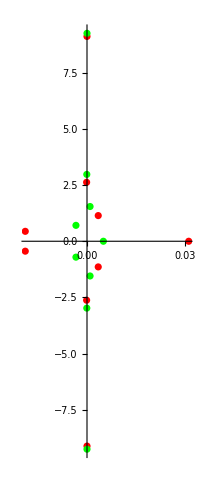

```mathematica
ComplexListPlot[{w[3],w[4]},PlotRange->All,PlotStyle->{Red,Green}]
```

```mathematica
w[1]=x/.NSolve[p[x]==0,x]
```

{0.618034,1.23607,2.,2.61803}

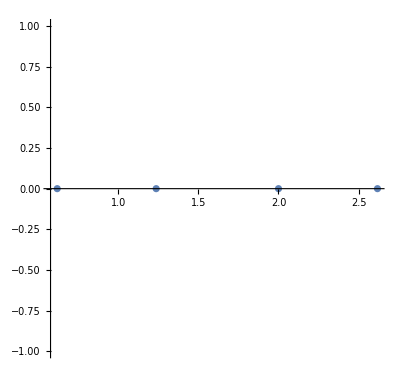

```mathematica
ComplexListPlot[w[1]]
```

```mathematica
w[2]=x/.NSolve[q[x]==0,x]
```

{1.61803-1. ⅈ,1.61803+1. ⅈ,1.61803-0.381966 ⅈ,1.61803+0.381966 ⅈ}

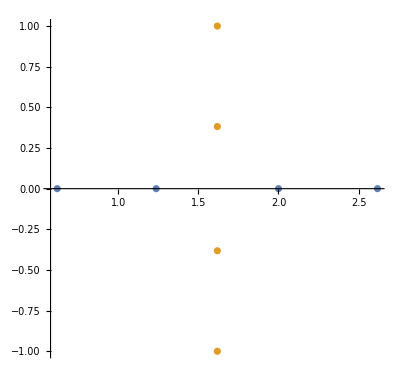

```mathematica
ComplexListPlot[{w[1],w[2]}]
```

```mathematica
BA44c=BA4.BA4c
```

{{2.5+0.363271 ⅈ,-1.30902-0.951057 ⅈ,0.118034+0.363271 ⅈ,0.+0. ⅈ},{-0.690983-0.951057 ⅈ,2.61803+0.726543 ⅈ,-1.30902-0.951057 ⅈ,0.118034+0.363271 ⅈ},{-0.118034+0.363271 ⅈ,-0.690983-0.951057 ⅈ,2.61803+0.726543 ⅈ,-1.30902-0.951057 ⅈ},{0.+0. ⅈ,-0.118034+0.363271 ⅈ,-0.690983-0.951057 ⅈ,2.73607+0.363271 ⅈ}}

```mathematica
Det[BA44c]//Chop
```

40.

```mathematica
Tr[BA44c]
```

10.4721+2.17963 ⅈ

```mathematica
u[3]=N[Eigenvalues[BA44c]]
```

{4.20019+2.5555 ⅈ,3.2196+0.711906 ⅈ,2.03047-0.497096 ⅈ,1.02188-0.590682 ⅈ}

```mathematica
s[x_]=CharacteristicPolynomial[BA44c,x]//Chop
```

40.-(66.7214+14.6619 ⅈ) x+(39.6869+11.4127 ⅈ) x^2-(10.4721+2.17963 ⅈ) x^3+x^4

```mathematica
o[z_,3]=Integrate[s[x]^2,{x,-z,z}]
```

(0.+0. ⅈ)+3200. z+(4941.15+1913.02 ⅈ) z^3+(1143.33+601.522 ⅈ) z^5+(52.6539+19.5646 ⅈ) z^7+0.222222 z^9

```mathematica
o[z_,4]=Integrate[p[x]*q[z],{x,-z,z}]
```

0.+80. z-165.22 z^2+231.915 z^3-252.276 z^4+175.623 z^5-71.0938 z^6+16.4498 z^7-2.58885 z^8+(2 z^9)/5

```mathematica
w[5]=z/.NSolve[o[z,4]==0,z]
```

{0.,0.-0.924176 ⅈ,0.+0.924176 ⅈ,0.-4.83905 ⅈ,0.+4.83905 ⅈ,1.61803-0.381966 ⅈ,1.61803+0.381966 ⅈ,1.61803-1. ⅈ,1.61803+1. ⅈ}

```mathematica
w[6]=z/.NSolve[o[z,3]-1==0,z]
```

{-2.87264+14.8429 ⅈ,-0.405396+4.48559 ⅈ,-0.18101-0.829483 ⅈ,-0.138273-2.07125 ⅈ,0.0003125-1.8244×10^-11 ⅈ,0.138344+2.07122 ⅈ,0.180628+0.829514 ⅈ,0.405394-4.48558 ⅈ,2.87264-14.8429 ⅈ}

```mathematica
(*root test as ones and zero*)
```

```mathematica
FullSimplify[Table[o[w[3][[j]],1],{j,Length[w[3]]}]]//Chop
```

{1.,1.,1.,1.,1.+9.37143×10^-9 ⅈ,1.-9.37143×10^-9 ⅈ,1.,1.,1.}

```mathematica
FullSimplify[Table[o[w[4][[j]],2],{j,Length[w[4]]}]]//Chop
```

{1.,1.,1.,1.,1.+6.15837×10^-8 ⅈ,1.-6.15837×10^-8 ⅈ,1.,1.,1.}

```mathematica
FullSimplify[Table[o[w[5][[j]],4],{j,Length[w[4]]}]]//Chop
```

{0,0,0,-2.03727×10^-10-3.74712×10^-10 ⅈ,-2.03727×10^-10+3.74712×10^-10 ⅈ,0,0,0,0}

```mathematica
FullSimplify[Table[o[w[6][[j]],3],{j,Length[w[6]]}]]//Chop
```

{0.999999+1.58139×10^-6 ⅈ,1.-4.07454×10^-10 ⅈ,1.,1.,1.,1.,1.,1.,0.999998-1.35414×10^-6 ⅈ}

```mathematica
ph[x_,1]=x^2*q[x]/p[x]
```

(x^2 (10.-20.6525 x+16.8541 x^2-6.47214 x^3+x^4))/(4.-13.2361 x+14.5623 x^2-6.47214 x^3+x^4)

```mathematica
ph[z_,2]=z^2*(o[z,2]-1)/(o[z,1]-1)
```

(z^2 (-1.+200. z+509.071 z^3+228.557 z^5+21.5991 z^7+0.222222 z^9))/(-1.+32. z+194.461 z^3+156.557 z^5+20.2895 z^7+0.222222 z^9)

```mathematica
g1=JuliaSetPlot[ph[x,1]/N[2],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False];
```

```mathematica
g2=ListPlot[JuliaSetPoints[ph[x,1]/N[2],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1];
```

```mathematica
Export["Julia_BA_4_Hermanrings_scale2_both.jpg",{g1,g2}]
```

Julia_BA_4_Hermanrings_scale2_both.jpg

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*scaled Hyper A_4   Herman rings*)
```

```mathematica
f[x_]=(x^2 (10-20.652475842498525 x+16.854101966249683 x^2-6.47213595499958 x^3+x^4))/(4.-13.23606797749979 x+14.562305898749052 x^2-6.47213595499958 x^3+x^4)
```

(x^2 (10-20.6525 x+16.8541 x^2-6.47214 x^3+x^4))/(4.-13.2361 x+14.5623 x^2-6.47214 x^3+x^4)

```mathematica
(*Mandelbrot with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Nov 2026 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 1024) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz]/2.;
		++escapeCount
	];
	escapeCount*(1-Abs[Arg[nz]/(2*Pi)])
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-2.75,3.25,1000},{-3.0,3.0,1000}}];
```

```mathematica
g1=ListPlot3D[Log[1/Max[arraym]+arraym], Mesh -> False,AspectRatio -> 1,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->3000];
```

```mathematica
Export["j_1000_BA_4_Hermanrings_scale2_Arg_Monitor_g1.jpg",g1]
```

j_1000_BA_4_Hermanrings_scale2_Arg_Monitor_g1.jpg

```mathematica
arraym=FractalPureM[{{-2.5,3.5,2000},{-3.0,3.0,2000}}];
```

```mathematica
g2=ListDensityPlot[Abs[Log[1+arraym]],Mesh -> False,AspectRatio -> 1,ColorFunction->"Rainbow",ImageSize->3000,Frame->False];
```

```mathematica
Export["j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_g2.jpg",g2]
```

j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_g2.jpg

```mathematica
g3=ListDensityPlot[arraym,Mesh -> False, AspectRatio -> 1, ColorFunction->"DarkBands",ImageSize->3000,Frame->False];
```

```mathematica
Export["j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_g3.jpg",g3]
```

j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_g3.jpg

```mathematica
g4=ListDensityPlot[arraym, Mesh -> False, AspectRatio -> 1,ColorFunction->(Hue[#]&),ImageSize->3000,Axes->False,Frame->False];
```

```mathematica
Export["j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_g4.jpg",g4]
```

j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_g4.jpg

```mathematica
g5=ListDensityPlot[Log[1/Max[arraym]+arraym],Mesh -> False, AspectRatio ->1, ColorFunction->(Hue[#*1.125]&),ImageSize->3000,Axes->False,Frame->False];
```

```mathematica
Export["j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_g5.jpg",g5]
```

j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_g5.jpg

```mathematica
(*Fonction pour colorier des isocontours,exemple d'utilisation typique:ContourPlot[T[x,y],{x,-10,10},{y,-10,10},ColorFunction->cf]*)
(*http://perso.ensem.inpl-nancy.fr/Emmanuel.Plaut/mathematica/mycolorfunction.m*)
colortab=Union[Join[{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.25,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
ln=Length[colortab]
```

254

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/ln,1,Ceiling[ln* l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g6=ListDensityPlot[Log[1/Max[arraym]+arraym], Mesh -> False, AspectRatio -> 1, ColorFunction->cf,ImageSize->3000,Frame->False];
```

```mathematica
Export["j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_g6.jpg",g6]
```

j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_g6.jpg

```mathematica
Export["j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_grid.jpg",GraphicsGrid[{{g1,g2}, 
 {g3,g4},{g5,g6}},ImageSize->{6000,9000}]]
```

j_1500_BA_4_Hermanrings_scale2_Arg_Monitor_grid.jpg

```mathematica
(*end*)
```